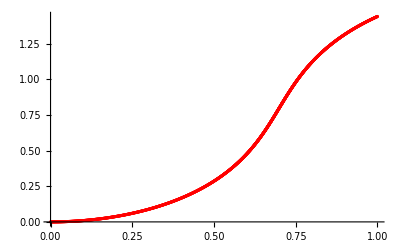

```mathematica
(*Тук май не трябват промени*)
RK4[f_,t0_,T_,u0_,h_]:=(
p1=1/6;
p2=1/3;
p3=1/3;
p4=1/6;

n=Ceiling[(T-t0)/h];
tc=t0;
uc=u0;
res=Table[0,n+1];
res[[1]]=u0;

For[k=1,k≤n,k++,

k1=h*f[tc,uc];
k2=h*f[tc+1/2*h,uc+1/2*k1];
k3=h*f[tc+1/2*h,uc+1/2*k2];
k4=h*f[tc+h,uc+k3];

res[[k+1]]=res[[k]]+p1*k1+p2*k2+p3*k3+p4*k4;
tc=tc+h;
uc=res[[k+1]];
];

res)

(*Отчитаме, че трябва да смятаме до r=1 и не знаем колко точно стъпки ще са необходими*)
(*Всеки ред от func е решение за дадено s, затова и после транспонираме при сметките*)
AB4Droplet[f_,s0_,u0_,h_]:=(
res2=Table[0,4];
RKapprox=RK4[f,s0,s0+3*h,u0,h];
For[it=1,it≤4,it++,res2[[it]]=RKapprox[[it]]];

sc=s0+3*h;
ucd=res2[[4]];

func=Table[f[s0+kk*h,res2[[kk+1]]],{kk,0,3}];
coeffs=List[-3/8,37/24,-59/24,55/24];

While[ucd[[1]]<1,
ucd=ucd+h*Transpose[func].coeffs;

AppendTo[res2,ucd];
sc=sc+h;

func=RotateLeft[func,1];
func[[4]]=f[sc,ucd];
];

res2
)

(*Условие*)
b=1.84366;
c=-2.9;
f[s_,u_List]:={Cos[u[[3]]],Sin[u[[3]]],If[s==0,b,2*b+c*u[[2]]-Sin[u[[3]]]/u[[1]]]};
s0=0;
u0={0,0,0};
h=0.001;

(*Решение*)
u=AB4Droplet[f,s0,u0,h];
ndrop=Length[u];

ListPlot[Table[{u[[k]][[1]],u[[k]][[2]]},{k,1,ndrop}],PlotStyle->Red]
```